# Lin-Kernighan O()

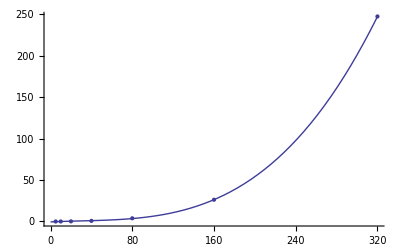

-0.481964+0.0563547 x-0.000853686 x^2+9.67681×10^-6 x^3

```mathematica
n={5,10,20,40,80,160,320};
t = {0.01, 0.04, 0.16, 0.73, 3.85, 26.23, 247.23};
data = Transpose[{n,t}];
l=ListPlot[data,AxesOrigin->{-10,-10}];
f=Fit[data,{1,x,x^2,x^3},x];
Show[l,Plot[f,{x,0,320}],AxesOrigin->{-10,-10}]
f
```